## Four-Equations, explicit resources and predator

```mathematica
dRdt=r*R*(1-R/K)-fc*R*C
dCdt=ec*fc*R*C-fp*C*P+α*(1-2*R/K)
dDdt=-α*(1-2*R/K)-fp*D*P
dPdt=ep*fp*C*P+ed*fp*D*P-d
```

-C fc R+r R (1-R/K)

-C fp P+C ec fc R+(1-(2 R)/K) α

-D fp P-(1-(2 R)/K) α

-d+D ed fp P+C ep fp P

```mathematica
Equil=FullSimplify[Solve[{dRdt==0,dCdt==0,dDdt==0,dPdt==0},{R,C,D,P}]]
```

{{R→1/2 (K+(2 (ed-ep) fc fp r α (-d+ed α)+√(fc^2 fp^2 r^2 (d-ed α)^2 (ec ep K r (-4 d+ec ep K r)+4 (ed-ep)^2 α^2)))/(ec ep fc fp r^2 (-d+ed α))),C→(fc fp r (d-ed α) (ec ep K r+2 (-ed+ep) α)+√(fc^2 fp^2 r^2 (d-ed α)^2 (ec ep K r (-4 d+ec ep K r)+4 (ed-ep)^2 α^2)))/(2 ec ep fc^2 fp K r (d-ed α)),D→(2 fp r^2 (-4 d+ec ep K r) α (d-ed α) (d+(-ed+ep) α))/(-8 d (ed-ep) fc fp r α^2 (d-ed α)+ec^2 ep fc fp K^2 r^3 (d-ed α)^2-2 ec fc fp K r^2 (d-ed α)^2 (2 d+(ed-ep) α)-d ec K r √(fc^2 fp^2 r^2 (d-ed α)^2 (ec ep K r (-4 d+ec ep K r)+4 (ed-ep)^2 α^2))-4 d α √(fc^2 fp^2 r^2 (d-ed α)^2 (ec ep K r (-4 d+ec ep K r)+4 (ed-ep)^2 α^2))+ec ed K r α √(fc^2 fp^2 r^2 (d-ed α)^2 (ec ep K r (-4 d+ec ep K r)+4 (ed-ep)^2 α^2))),P→(-√(fc^2 fp^2 r^2 (d-ed α)^2 (ec ep K r (-4 d+ec ep K r)+4 (ed-ep)^2 α^2))+fc fp r (d ec ep K r+2 d (ed+ep) α-ed α (ec ep K r+2 (ed-ep) α)))/(2 ep fp^2 r^2 (d+(-ed+ep) α))},{R→(fc fp r (d-ed α) (ec ep K r+2 (ed-ep) α)+√(fc^2 fp^2 r^2 (d-ed α)^2 (ec ep K r (-4 d+ec ep K r)+4 (ed-ep)^2 α^2)))/(2 ec ep fc fp r^2 (d-ed α)),C→(fc fp r (d-ed α) (ec ep K r+2 (-ed+ep) α)-√(fc^2 fp^2 r^2 (d-ed α)^2 (ec ep K r (-4 d+ec ep K r)+4 (ed-ep)^2 α^2)))/(2 ec ep fc^2 fp K r (d-ed α)),D→(2 fp r^2 (-4 d+ec ep K r) α (d-ed α) (d+(-ed+ep) α))/(-8 d (ed-ep) fc fp r α^2 (d-ed α)+ec^2 ep fc fp K^2 r^3 (d-ed α)^2-2 ec fc fp K r^2 (d-ed α)^2 (2 d+(ed-ep) α)+d ec K r √(fc^2 fp^2 r^2 (d-ed α)^2 (ec ep K r (-4 d+ec ep K r)+4 (ed-ep)^2 α^2))+4 d α √(fc^2 fp^2 r^2 (d-ed α)^2 (ec ep K r (-4 d+ec ep K r)+4 (ed-ep)^2 α^2))-ec ed K r α √(fc^2 fp^2 r^2 (d-ed α)^2 (ec ep K r (-4 d+ec ep K r)+4 (ed-ep)^2 α^2))),P→(√(fc^2 fp^2 r^2 (d-ed α)^2 (ec ep K r (-4 d+ec ep K r)+4 (ed-ep)^2 α^2))+fc fp r (d ec ep K r+2 d (ed+ep) α-ed α (ec ep K r+2 (ed-ep) α)))/(2 ep fp^2 r^2 (d+(-ed+ep) α))}}

```mathematica
JacGen={
{D[dRdt,R],D[dRdt,C],D[dRdt,D],D[dRdt,P]},
{D[dCdt,R],D[dCdt,C],D[dCdt,D],D[dCdt,P]},
{D[dDdt,R],D[dDdt,C],D[dDdt,D],D[dDdt,P]},
{D[dPdt,R],D[dPdt,C],D[dPdt,D],D[dPdt,P]}}
```

{{-C fc-(r R)/K+r (1-R/K),-fc R,0,0},{C ec fc-(2 α)/K,-fp P+ec fc R,0,-C fp},{(2 α)/K,0,-fp P,-D fp},{0,ep fp P,ed fp P,D ed fp+C ep fp}}

```mathematica
JacGen//MatrixForm
```

(-C fc-(r R)/K+r (1-R/K) | -fc R | 0 | 0
C ec fc-(2 α)/K | -fp P+ec fc R | 0 | -C fp
(2 α)/K | 0 | -fp P | -D fp
0 | ep fp P | ed fp P | D ed fp+C ep fp)

```mathematica
Jac1=JacGen/.Equil[[1]]
```

{{-((fc fp r (d-ed α) (ec ep K r+2 (-ed+ep) α)+√(fc^2 fp^2 r^2 (d-ed α)^2 (ec ep K r (-4 d+ec ep K r)+4 (ed-ep)^2 α^2)))/(2 ec ep fc fp K r (d-ed α)))-(r (K+(2 (ed-ep) fc fp r α (-d+ed α)+√(fc^2 fp^2 r^2 (d-ed α)^2 (ec ep K r (-4 d+ec ep K r)+4 (ed-ep)^2 α^2)))/(ec ep fc fp r^2 (-d+ed α))))/(2 K)+r (1-(K+(2 (ed-ep) fc fp r α (-d+ed α)+√(fc^2 fp^2 r^2 (d-ed α)^2 (ec ep K r (-4 d+ec ep K r)+4 (ed-ep)^2 α^2)))/(ec ep fc fp r^2 (-d+ed α)))/(2 K)),-1/2 fc (K+(2 (ed-ep) fc fp r α (-d+ed α)+√(fc^2 fp^2 r^2 (d-ed α)^2 (ec ep K r (-4 d+ec ep K r)+4 (ed-ep)^2 α^2)))/(ec ep fc fp r^2 (-d+ed α))),0,0},{-(2 α)/K+1/(2 ep fc fp K r (d-ed α))(fc fp r (d-ed α) (ec ep K r+2 (-ed+ep) α)+√(fc^2 fp^2 r^2 (d-ed α)^2 (ec ep K r (-4 d+ec ep K r)+4 (ed-ep)^2 α^2))),-((-√(fc^2 fp^2 r^2 (d-ed α)^2 (ec ep K r (-4 d+ec ep K r)+4 (ed-ep)^2 α^2))+fc fp r (d ec ep K r+2 d (ed+ep) α-ed α (ec ep K r+2 (ed-ep) α)))/(2 ep fp r^2 (d+(-ed+ep) α)))+1/2 ec fc (K+(2 (ed-ep) fc fp r α (-d+ed α)+√(fc^2 fp^2 r^2 (d-ed α)^2 (ec ep K r (-4 d+ec ep K r)+4 (ed-ep)^2 α^2)))/(ec ep fc fp r^2 (-d+ed α))),0,-1/(2 ec ep fc^2 K r (d-ed α))(fc fp r (d-ed α) (ec ep K r+2 (-ed+ep) α)+√(fc^2 fp^2 r^2 (d-ed α)^2 (ec ep K r (-4 d+ec ep K r)+4 (ed-ep)^2 α^2)))},{(2 α)/K,0,-((-√(fc^2 fp^2 r^2 (d-ed α)^2 (ec ep K r (-4 d+ec ep K r)+4 (ed-ep)^2 α^2))+fc fp r (d ec ep K r+2 d (ed+ep) α-ed α (ec ep K r+2 (ed-ep) α)))/(2 ep fp r^2 (d+(-ed+ep) α))),-((2 fp^2 r^2 (-4 d+ec ep K r) α (d-ed α) (d+(-ed+ep) α))/(-8 d (ed-ep) fc fp r α^2 (d-ed α)+ec^2 ep fc fp K^2 r^3 (d-ed α)^2-2 ec fc fp K r^2 (d-ed α)^2 (2 d+(ed-ep) α)-d ec K r √(fc^2 fp^2 r^2 (d-ed α)^2 (ec ep K r (-4 d+ec ep K r)+4 (ed-ep)^2 α^2))-4 d α √(fc^2 fp^2 r^2 (d-ed α)^2 (ec ep K r (-4 d+ec ep K r)+4 (ed-ep)^2 α^2))+ec ed K r α √(fc^2 fp^2 r^2 (d-ed α)^2 (ec ep K r (-4 d+ec ep K r)+4 (ed-ep)^2 α^2))))},{0,(-√(fc^2 fp^2 r^2 (d-ed α)^2 (ec ep K r (-4 d+ec ep K r)+4 (ed-ep)^2 α^2))+fc fp r (d ec ep K r+2 d (ed+ep) α-ed α (ec ep K r+2 (ed-ep) α)))/(2 fp r^2 (d+(-ed+ep) α)),(ed (-√(fc^2 fp^2 r^2 (d-ed α)^2 (ec ep K r (-4 d+ec ep K r)+4 (ed-ep)^2 α^2))+fc fp r (d ec ep K r+2 d (ed+ep) α-ed α (ec ep K r+2 (ed-ep) α))))/(2 ep fp r^2 (d+(-ed+ep) α)),1/(2 ec fc^2 K r (d-ed α))(fc fp r (d-ed α) (ec ep K r+2 (-ed+ep) α)+√(fc^2 fp^2 r^2 (d-ed α)^2 (ec ep K r (-4 d+ec ep K r)+4 (ed-ep)^2 α^2)))+(2 ed fp^2 r^2 (-4 d+ec ep K r) α (d-ed α) (d+(-ed+ep) α))/(-8 d (ed-ep) fc fp r α^2 (d-ed α)+ec^2 ep fc fp K^2 r^3 (d-ed α)^2-2 ec fc fp K r^2 (d-ed α)^2 (2 d+(ed-ep) α)-d ec K r √(fc^2 fp^2 r^2 (d-ed α)^2 (ec ep K r (-4 d+ec ep K r)+4 (ed-ep)^2 α^2))-4 d α √(fc^2 fp^2 r^2 (d-ed α)^2 (ec ep K r (-4 d+ec ep K r)+4 (ed-ep)^2 α^2))+ec ed K r α √(fc^2 fp^2 r^2 (d-ed α)^2 (ec ep K r (-4 d+ec ep K r)+4 (ed-ep)^2 α^2)))}}

```mathematica
Jac2=JacGen/.Equil[[2]]
```

{{-((fc fp r (d-ed α) (ec ep K r+2 (-ed+ep) α)-√(fc^2 fp^2 r^2 (d-ed α)^2 (ec ep K r (-4 d+ec ep K r)+4 (ed-ep)^2 α^2)))/(2 ec ep fc fp K r (d-ed α)))-(fc fp r (d-ed α) (ec ep K r+2 (ed-ep) α)+√(fc^2 fp^2 r^2 (d-ed α)^2 (ec ep K r (-4 d+ec ep K r)+4 (ed-ep)^2 α^2)))/(2 ec ep fc fp K r (d-ed α))+r (1-(fc fp r (d-ed α) (ec ep K r+2 (ed-ep) α)+√(fc^2 fp^2 r^2 (d-ed α)^2 (ec ep K r (-4 d+ec ep K r)+4 (ed-ep)^2 α^2)))/(2 ec ep fc fp K r^2 (d-ed α))),-1/(2 ec ep fp r^2 (d-ed α))(fc fp r (d-ed α) (ec ep K r+2 (ed-ep) α)+√(fc^2 fp^2 r^2 (d-ed α)^2 (ec ep K r (-4 d+ec ep K r)+4 (ed-ep)^2 α^2))),0,0},{-(2 α)/K+1/(2 ep fc fp K r (d-ed α))(fc fp r (d-ed α) (ec ep K r+2 (-ed+ep) α)-√(fc^2 fp^2 r^2 (d-ed α)^2 (ec ep K r (-4 d+ec ep K r)+4 (ed-ep)^2 α^2))),1/(2 ep fp r^2 (d-ed α))(fc fp r (d-ed α) (ec ep K r+2 (ed-ep) α)+√(fc^2 fp^2 r^2 (d-ed α)^2 (ec ep K r (-4 d+ec ep K r)+4 (ed-ep)^2 α^2)))-(√(fc^2 fp^2 r^2 (d-ed α)^2 (ec ep K r (-4 d+ec ep K r)+4 (ed-ep)^2 α^2))+fc fp r (d ec ep K r+2 d (ed+ep) α-ed α (ec ep K r+2 (ed-ep) α)))/(2 ep fp r^2 (d+(-ed+ep) α)),0,-1/(2 ec ep fc^2 K r (d-ed α))(fc fp r (d-ed α) (ec ep K r+2 (-ed+ep) α)-√(fc^2 fp^2 r^2 (d-ed α)^2 (ec ep K r (-4 d+ec ep K r)+4 (ed-ep)^2 α^2)))},{(2 α)/K,0,-((√(fc^2 fp^2 r^2 (d-ed α)^2 (ec ep K r (-4 d+ec ep K r)+4 (ed-ep)^2 α^2))+fc fp r (d ec ep K r+2 d (ed+ep) α-ed α (ec ep K r+2 (ed-ep) α)))/(2 ep fp r^2 (d+(-ed+ep) α))),-((2 fp^2 r^2 (-4 d+ec ep K r) α (d-ed α) (d+(-ed+ep) α))/(-8 d (ed-ep) fc fp r α^2 (d-ed α)+ec^2 ep fc fp K^2 r^3 (d-ed α)^2-2 ec fc fp K r^2 (d-ed α)^2 (2 d+(ed-ep) α)+d ec K r √(fc^2 fp^2 r^2 (d-ed α)^2 (ec ep K r (-4 d+ec ep K r)+4 (ed-ep)^2 α^2))+4 d α √(fc^2 fp^2 r^2 (d-ed α)^2 (ec ep K r (-4 d+ec ep K r)+4 (ed-ep)^2 α^2))-ec ed K r α √(fc^2 fp^2 r^2 (d-ed α)^2 (ec ep K r (-4 d+ec ep K r)+4 (ed-ep)^2 α^2))))},{0,(√(fc^2 fp^2 r^2 (d-ed α)^2 (ec ep K r (-4 d+ec ep K r)+4 (ed-ep)^2 α^2))+fc fp r (d ec ep K r+2 d (ed+ep) α-ed α (ec ep K r+2 (ed-ep) α)))/(2 fp r^2 (d+(-ed+ep) α)),(ed (√(fc^2 fp^2 r^2 (d-ed α)^2 (ec ep K r (-4 d+ec ep K r)+4 (ed-ep)^2 α^2))+fc fp r (d ec ep K r+2 d (ed+ep) α-ed α (ec ep K r+2 (ed-ep) α))))/(2 ep fp r^2 (d+(-ed+ep) α)),1/(2 ec fc^2 K r (d-ed α))(fc fp r (d-ed α) (ec ep K r+2 (-ed+ep) α)-√(fc^2 fp^2 r^2 (d-ed α)^2 (ec ep K r (-4 d+ec ep K r)+4 (ed-ep)^2 α^2)))+(2 ed fp^2 r^2 (-4 d+ec ep K r) α (d-ed α) (d+(-ed+ep) α))/(-8 d (ed-ep) fc fp r α^2 (d-ed α)+ec^2 ep fc fp K^2 r^3 (d-ed α)^2-2 ec fc fp K r^2 (d-ed α)^2 (2 d+(ed-ep) α)+d ec K r √(fc^2 fp^2 r^2 (d-ed α)^2 (ec ep K r (-4 d+ec ep K r)+4 (ed-ep)^2 α^2))+4 d α √(fc^2 fp^2 r^2 (d-ed α)^2 (ec ep K r (-4 d+ec ep K r)+4 (ed-ep)^2 α^2))-ec ed K r α √(fc^2 fp^2 r^2 (d-ed α)^2 (ec ep K r (-4 d+ec ep K r)+4 (ed-ep)^2 α^2)))}}

```mathematica
Eigs1=FullSimplify[Eigenvalues[Jac1]]
```

$Aborted

## No-predator, Implicit Resources, Stochastic Resuscitation

```mathematica
R=1-A*(Subscript[γ, g]+Subscript[γ, m])-D*Subscript[γ, m]
dAdt=R*r*A*(Subscript[γ, g]+Subscript[γ, m])-Subscript[δ, max]*(1-R)*A*(Subscript[γ, g]+Subscript[γ, m])+α*D*Subscript[γ, m]-Subscript[m, a]*A*(Subscript[γ, g]+Subscript[γ, m])
dDdt=Subscript[δ, max]*(1-R)*A*(Subscript[γ, g]+Subscript[γ, m])-α*D*Subscript[γ, m]-Subscript[m, d]*D*Subscript[γ, m]
```

1-D γ_m-A (γ_g+γ_m)

D α γ_m-A m_a (γ_g+γ_m)+A r (γ_g+γ_m) (1-D γ_m-A (γ_g+γ_m))-A (γ_g+γ_m) (D γ_m+A (γ_g+γ_m)) δ_max

-D α γ_m-D m_d γ_m+A (γ_g+γ_m) (D γ_m+A (γ_g+γ_m)) δ_max

```mathematica
Equil=FullSimplify[Solve[{dAdt==0,dDdt==0},{A,D}]]
```

{{A→0,D→0},{A→((r-m_a) (α+m_d))/((γ_g+γ_m) (r (α+m_d)+(r-m_a+m_d) δ_max)),D→((r-m_a)^2 (α+m_d) δ_max)/(γ_m (r (α+m_d)+(r-m_a+m_d) δ_max) (r α+m_d (r+δ_max)))}}

```mathematica
JacGen={
{D[dAdt,A],D[dAdt,D]},
{D[dDdt,A],D[dDdt,D]}}
```

{{-m_a (γ_g+γ_m)+A r (-γ_g-γ_m) (γ_g+γ_m)+r (γ_g+γ_m) (1-D γ_m-A (γ_g+γ_m))-A (γ_g+γ_m)^2 δ_max-(γ_g+γ_m) (D γ_m+A (γ_g+γ_m)) δ_max,α γ_m-A r γ_m (γ_g+γ_m)-A γ_m (γ_g+γ_m) δ_max},{A (γ_g+γ_m)^2 δ_max+(γ_g+γ_m) (D γ_m+A (γ_g+γ_m)) δ_max,-α γ_m-m_d γ_m+A γ_m (γ_g+γ_m) δ_max}}

```mathematica
Jtriv=JacGen/.Equil[[1]]
```

{{r (γ_g+γ_m)-m_a (γ_g+γ_m),α γ_m},{0,-α γ_m-m_d γ_m}}

```mathematica
Jint=JacGen/.Equil[[2]]
```

{{-m_a (γ_g+γ_m)+(r (r-m_a) (α+m_d) (-γ_g-γ_m))/(r (α+m_d)+(r-m_a+m_d) δ_max)-((r-m_a) (α+m_d) (γ_g+γ_m) δ_max)/(r (α+m_d)+(r-m_a+m_d) δ_max)+r (γ_g+γ_m) (1-((r-m_a) (α+m_d))/(r (α+m_d)+(r-m_a+m_d) δ_max)-((r-m_a)^2 (α+m_d) δ_max)/((r (α+m_d)+(r-m_a+m_d) δ_max) (r α+m_d (r+δ_max))))-(γ_g+γ_m) δ_max (((r-m_a) (α+m_d))/(r (α+m_d)+(r-m_a+m_d) δ_max)+((r-m_a)^2 (α+m_d) δ_max)/((r (α+m_d)+(r-m_a+m_d) δ_max) (r α+m_d (r+δ_max)))),α γ_m-(r (r-m_a) (α+m_d) γ_m)/(r (α+m_d)+(r-m_a+m_d) δ_max)-((r-m_a) (α+m_d) γ_m δ_max)/(r (α+m_d)+(r-m_a+m_d) δ_max)},{((r-m_a) (α+m_d) (γ_g+γ_m) δ_max)/(r (α+m_d)+(r-m_a+m_d) δ_max)+(γ_g+γ_m) δ_max (((r-m_a) (α+m_d))/(r (α+m_d)+(r-m_a+m_d) δ_max)+((r-m_a)^2 (α+m_d) δ_max)/((r (α+m_d)+(r-m_a+m_d) δ_max) (r α+m_d (r+δ_max)))),-α γ_m-m_d γ_m+((r-m_a) (α+m_d) γ_m δ_max)/(r (α+m_d)+(r-m_a+m_d) δ_max)}}

```mathematica
FullSimplify[Jtriv//Eigenvalues]
```

{-(α+m_d) γ_m,(r-m_a) (γ_g+γ_m)}

```mathematica
A1=FullSimplify[-Tr[Jint]]
A2=FullSimplify[Det[Jint]]
```

((r-m_a) γ_g (r^2 (α+m_d)^2+2 r (α+m_d)^2 δ_max+(r α-α m_a+2 α m_d+m_d^2) δ_max^2)+γ_m (r^2 (α+m_d)^2 (r+α-m_a+m_d)+2 r (α+m_d)^2 (r-m_a+m_d) δ_max+(r-m_a+m_d) (r α-α m_a+m_d (α+m_d)) δ_max^2))/((r (α+m_d)+(r-m_a+m_d) δ_max) (r α+m_d (r+δ_max)))

(r-m_a) (α+m_d) γ_m (γ_g+γ_m)

```mathematica
Solve[A1==0,Subscript[m, a]]
```

{{m_a→1/(2 (α γ_g δ_max^2+α γ_m δ_max^2))(r^2 α^2 γ_g+2 r^2 α m_d γ_g+r^2 m_d^2 γ_g+r^2 α^2 γ_m+2 r^2 α m_d γ_m+r^2 m_d^2 γ_m+2 r α^2 γ_g δ_max+4 r α m_d γ_g δ_max+2 r m_d^2 γ_g δ_max+2 r α^2 γ_m δ_max+4 r α m_d γ_m δ_max+2 r m_d^2 γ_m δ_max+2 r α γ_g δ_max^2+2 α m_d γ_g δ_max^2+m_d^2 γ_g δ_max^2+2 r α γ_m δ_max^2+2 α m_d γ_m δ_max^2+m_d^2 γ_m δ_max^2-(r α+r m_d+m_d δ_max) √(r^2 α^2 γ_g^2+2 r^2 α m_d γ_g^2+r^2 m_d^2 γ_g^2+2 r^2 α^2 γ_g γ_m+4 r^2 α m_d γ_g γ_m+2 r^2 m_d^2 γ_g γ_m+r^2 α^2 γ_m^2+2 r^2 α m_d γ_m^2+r^2 m_d^2 γ_m^2+4 r α^2 γ_g^2 δ_max+6 r α m_d γ_g^2 δ_max+2 r m_d^2 γ_g^2 δ_max+8 r α^2 γ_g γ_m δ_max+12 r α m_d γ_g γ_m δ_max+4 r m_d^2 γ_g γ_m δ_max+4 r α^2 γ_m^2 δ_max+6 r α m_d γ_m^2 δ_max+2 r m_d^2 γ_m^2 δ_max+4 α^2 γ_g^2 δ_max^2+4 α m_d γ_g^2 δ_max^2+m_d^2 γ_g^2 δ_max^2+4 α^2 γ_g γ_m δ_max^2+4 α m_d γ_g γ_m δ_max^2+2 m_d^2 γ_g γ_m δ_max^2+m_d^2 γ_m^2 δ_max^2))},{m_a→1/(2 (α γ_g δ_max^2+α γ_m δ_max^2))(r^2 α^2 γ_g+2 r^2 α m_d γ_g+r^2 m_d^2 γ_g+r^2 α^2 γ_m+2 r^2 α m_d γ_m+r^2 m_d^2 γ_m+2 r α^2 γ_g δ_max+4 r α m_d γ_g δ_max+2 r m_d^2 γ_g δ_max+2 r α^2 γ_m δ_max+4 r α m_d γ_m δ_max+2 r m_d^2 γ_m δ_max+2 r α γ_g δ_max^2+2 α m_d γ_g δ_max^2+m_d^2 γ_g δ_max^2+2 r α γ_m δ_max^2+2 α m_d γ_m δ_max^2+m_d^2 γ_m δ_max^2+(r α+r m_d+m_d δ_max) √(r^2 α^2 γ_g^2+2 r^2 α m_d γ_g^2+r^2 m_d^2 γ_g^2+2 r^2 α^2 γ_g γ_m+4 r^2 α m_d γ_g γ_m+2 r^2 m_d^2 γ_g γ_m+r^2 α^2 γ_m^2+2 r^2 α m_d γ_m^2+r^2 m_d^2 γ_m^2+4 r α^2 γ_g^2 δ_max+6 r α m_d γ_g^2 δ_max+2 r m_d^2 γ_g^2 δ_max+8 r α^2 γ_g γ_m δ_max+12 r α m_d γ_g γ_m δ_max+4 r m_d^2 γ_g γ_m δ_max+4 r α^2 γ_m^2 δ_max+6 r α m_d γ_m^2 δ_max+2 r m_d^2 γ_m^2 δ_max+4 α^2 γ_g^2 δ_max^2+4 α m_d γ_g^2 δ_max^2+m_d^2 γ_g^2 δ_max^2+4 α^2 γ_g γ_m δ_max^2+4 α m_d γ_g γ_m δ_max^2+2 m_d^2 γ_g γ_m δ_max^2+m_d^2 γ_m^2 δ_max^2))}}

```mathematica
Parms={r->2,Subscript[γ, g]->.02,Subscript[γ, m]->.01,α->.03,Subscript[δ, max]->.1,Subscript[m, a]->.01,Subscript[m, d]->0.001}
```

{r→2,γ_g→0.02,γ_m→0.01,α→0.03,δ_max→0.1,m_a→0.01,m_d→0.001}

```mathematica
Amax=1/(Subscript[γ, m]+Subscript[γ, g])/.Parms;
Dmax=1/Subscript[γ, m]/.Parms;
```

```mathematica
Plot3D[dAdt/.Parms,{A,0,Amax},{D,0,Dmax},
AxesLabel->{"Active","Dormant","dA/dt"},
PlotRange->{{0,Amax},{0,Dmax},{0,.5}},
BaseStyle->{FontSize->18}]
```

-Graphics3D-

```mathematica
Plot3D[dDdt/.Parms,{A,0,Amax},{D,0,Dmax},
AxesLabel->{"Active","Dormant","dD/dt"},
PlotRange->{{0,Amax},{0,Dmax},{0,.25}},
BaseStyle->{FontSize->18}]
```

-Graphics3D-

```mathematica
StabParms={r->2,Subscript[γ, g]->.02,Subscript[γ, m]->.01,α->0.03,Subscript[δ, max]->.1}
Plot3D[A1/.StabParms,{Subscript[m, a],0,1},{Subscript[m, d],0,1},
AxesLabel->{"m_a","m_d","A1"},
PlotRange->{{0,1},{0,1},{0,.1}}]
```

{r→2,γ_g→0.02,γ_m→0.01,α→0.03,δ_max→0.1}

-Graphics3D-

```mathematica
Plot3D[{Equil[[2,1,2]]/.StabParms,Equil[[2,2,2]]/.StabParms}, {Subscript[m, a],0,1},{Subscript[m, d],0,1},
AxesLabel->{"Active Mortality Rate", "Dormant Mortality Rate","A* or P*"},
PlotStyle->{Red,Blue},PlotLegends->{"A*","D*"}]
```

-Graphics3D-

```mathematica
zngi1=FullSimplify[Solve[dAdt==0,D]];
```

```mathematica
zngi2=FullSimplify[Solve[dDdt==0,D]];
```

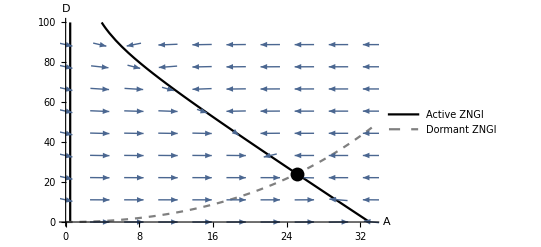

```mathematica
Iso=Plot[
{zngi1[[1,1,2]]/.Parms,
zngi2[[1,1,2]]/.Parms},{A,0,Amax},
AxesLabel->{"A","D"},
PlotStyle->{{Black,Thick},{Gray,Dashed}},
PlotRange->{{0,Amax},{0,Dmax}},
PlotLegends->{"Active ZNGI","Dormant ZNGI"},
BaseStyle->{FontSize->18}];
Vec=VectorPlot[{dAdt/.Parms,dDdt/.Parms},{A,0,Amax},{D,0,Dmax},VectorPoints->10,VectorScale->{.02,Scaled[.5],None}];
NC=Show[Iso,Vec,Graphics[{PointSize[0.025],Point[{Equil[[2,1,2]]/.Parms,Equil[[2,2,2]]/.Parms}]}]]
```

```mathematica
dAnum=a'[t]==d[t]*α*Subscript[γ, m]-a[t]* Subscript[m, a] *(Subscript[γ, g]+Subscript[γ, m])-a[t]* r *(Subscript[γ, g]+Subscript[γ, m])*(-1+a[t]*Subscript[γ, g]+(a[t]+d[t])*Subscript[γ, m])-a[t]*(Subscript[γ, g]+Subscript[γ, m])* (a[t]*Subscript[γ, g]+(a[t]+d[t])*Subscript[γ, m])* Subscript[δ, max];
dDnum=d'[t]==-d[t]*α*Subscript[γ, m]+a[t]*(Subscript[γ, g]+Subscript[γ, m])*(a[t]*Subscript[γ, g]+(a[t]+d[t])*Subscript[γ, m])* Subscript[δ, max]-Subscript[m, d]*d[t]*Subscript[γ, m];
```

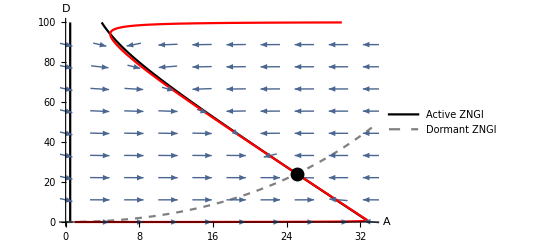

```mathematica
ADsolve1=NDSolve[{dAnum/.Parms,dDnum/.Parms,d[0]==0,a[0]==1},{a[t],d[t]},{t,0,10000}];
PlotADTime1=Plot[Evaluate[{a[t],d[t]}/.ADsolve1],{t,0,10000},PlotStyle->{{Black,Solid},{Gray,Dashed}},
PlotLegends->{"Active","Dormant"}];
PlotADTimePS1 = ParametricPlot[{a[t],d[t]}/.ADsolve1,{t,0,10000},PlotRange->{{0,Amax},{0,Dmax}},
AxesLabel->{"A","D"},
PlotStyle->{Red,Thick},
BaseStyle->{FontSize->18}];

ADsolve2=NDSolve[{dAnum/.Parms,dDnum/.Parms,d[0]==100,a[0]==30},{a[t],d[t]},{t,0,10000}];
PlotADTime2=Plot[Evaluate[{a[t],d[t]}/.ADsolve2],{t,0,10000},PlotStyle->{{Black,Solid},{Gray,Dashed}},
PlotLegends->{"Active","Dormant"}];
PlotADTimePS2 = ParametricPlot[{a[t],d[t]}/.ADsolve2,{t,0,10000},PlotRange->{{0,Amax},{0,Dmax}},
AxesLabel->{"A","D"},
PlotStyle->{Red,Thick},
BaseStyle->{FontSize->18}];

Show[NC,PlotADTimePS1,PlotADTimePS2]
```

## No-predator, Implicit Resources, Responsive Resuscitation

```mathematica
R=1-A*(Subscript[γ, g]+Subscript[γ, m])-D*Subscript[γ, m]
dAdt=R*r*A*(Subscript[γ, g]+Subscript[γ, m])-Subscript[δ, max]*(1-R)*A*(Subscript[γ, g]+Subscript[γ, m])+α*R*D*Subscript[γ, m]-Subscript[m, a]*A*(Subscript[γ, g]+Subscript[γ, m])
dDdt=Subscript[δ, max]*(1-R)*A*(Subscript[γ, g]+Subscript[γ, m])-α*R*D*Subscript[γ, m]-Subscript[m, d]*D*Subscript[γ, m]
```

1-D γ_m-A (γ_g+γ_m)

-A m_a (γ_g+γ_m)+D α γ_m (1-D γ_m-A (γ_g+γ_m))+A r (γ_g+γ_m) (1-D γ_m-A (γ_g+γ_m))-A (γ_g+γ_m) (D γ_m+A (γ_g+γ_m)) δ_max

-D m_d γ_m-D α γ_m (1-D γ_m-A (γ_g+γ_m))+A (γ_g+γ_m) (D γ_m+A (γ_g+γ_m)) δ_max

```mathematica
Equil=FullSimplify[Solve[{dAdt==0,dDdt==0},{A,D}]]
```

{{A→0,D→0},{A→-((α m_a^2+m_d^2 (r+δ_max)+r √((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2)+m_d (-r^2+2 r α+r δ_max+√((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2))-m_a (r α+m_d (-r+α+δ_max)+√((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2)))/(2 r (γ_g+γ_m) ((m_a-m_d) (α-δ_max)+r (m_d+δ_max)))),D→-(((α m_a+m_d (r+δ_max)+√((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2)) (-α m_a^2-m_d^2 (r+δ_max)-r √((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2)-m_d (-r^2+2 r α+r δ_max+√((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2))+m_a (r α+m_d (-r+α+δ_max)+√((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2))))/(4 r α m_d γ_m ((m_a-m_d) (α-δ_max)+r (m_d+δ_max))))},{A→(-α m_a^2-m_d^2 (r+δ_max)+r √((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2)+m_a (r α+m_d (-r+α+δ_max)-√((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2))+m_d (r^2-2 r α-r δ_max+√((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2)))/(2 r (γ_g+γ_m) ((m_a-m_d) (α-δ_max)+r (m_d+δ_max))),D→-(((α m_a+m_d (r+δ_max)-√((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2)) (-α m_a^2-m_d^2 (r+δ_max)+r √((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2)+m_a (r α+m_d (-r+α+δ_max)-√((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2))+m_d (r^2-2 r α-r δ_max+√((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2))))/(4 r α m_d γ_m ((m_a-m_d) (α-δ_max)+r (m_d+δ_max))))}}

```mathematica
JacGen={
{D[dAdt,A],D[dAdt,D]},
{D[dDdt,A],D[dDdt,D]}}
```

{{D α (-γ_g-γ_m) γ_m-m_a (γ_g+γ_m)+A r (-γ_g-γ_m) (γ_g+γ_m)+r (γ_g+γ_m) (1-D γ_m-A (γ_g+γ_m))-A (γ_g+γ_m)^2 δ_max-(γ_g+γ_m) (D γ_m+A (γ_g+γ_m)) δ_max,-D α γ_m^2-A r γ_m (γ_g+γ_m)+α γ_m (1-D γ_m-A (γ_g+γ_m))-A γ_m (γ_g+γ_m) δ_max},{-D α (-γ_g-γ_m) γ_m+A (γ_g+γ_m)^2 δ_max+(γ_g+γ_m) (D γ_m+A (γ_g+γ_m)) δ_max,-m_d γ_m+D α γ_m^2-α γ_m (1-D γ_m-A (γ_g+γ_m))+A γ_m (γ_g+γ_m) δ_max}}

```mathematica
Jtriv=JacGen/.Equil[[1]]
```

{{r (γ_g+γ_m)-m_a (γ_g+γ_m),α γ_m},{0,-α γ_m-m_d γ_m}}

```mathematica
Jint=JacGen/.Equil[[2]]
```

{{-m_a (γ_g+γ_m)-1/(2 ((m_a-m_d) (α-δ_max)+r (m_d+δ_max)))(-γ_g-γ_m) (α m_a^2+m_d^2 (r+δ_max)+r √((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2)+m_d (-r^2+2 r α+r δ_max+√((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2))-m_a (r α+m_d (-r+α+δ_max)+√((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2)))+1/(2 r ((m_a-m_d) (α-δ_max)+r (m_d+δ_max)))(γ_g+γ_m) δ_max (α m_a^2+m_d^2 (r+δ_max)+r √((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2)+m_d (-r^2+2 r α+r δ_max+√((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2))-m_a (r α+m_d (-r+α+δ_max)+√((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2)))-((-γ_g-γ_m) (α m_a+m_d (r+δ_max)+√((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2)) (-α m_a^2-m_d^2 (r+δ_max)-r √((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2)-m_d (-r^2+2 r α+r δ_max+√((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2))+m_a (r α+m_d (-r+α+δ_max)+√((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2))))/(4 r m_d ((m_a-m_d) (α-δ_max)+r (m_d+δ_max)))-(γ_g+γ_m) δ_max (-1/(2 r ((m_a-m_d) (α-δ_max)+r (m_d+δ_max)))(α m_a^2+m_d^2 (r+δ_max)+r √((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2)+m_d (-r^2+2 r α+r δ_max+√((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2))-m_a (r α+m_d (-r+α+δ_max)+√((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2)))-((α m_a+m_d (r+δ_max)+√((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2)) (-α m_a^2-m_d^2 (r+δ_max)-r √((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2)-m_d (-r^2+2 r α+r δ_max+√((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2))+m_a (r α+m_d (-r+α+δ_max)+√((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2))))/(4 r α m_d ((m_a-m_d) (α-δ_max)+r (m_d+δ_max))))+r (γ_g+γ_m) (1+1/(2 r ((m_a-m_d) (α-δ_max)+r (m_d+δ_max)))(α m_a^2+m_d^2 (r+δ_max)+r √((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2)+m_d (-r^2+2 r α+r δ_max+√((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2))-m_a (r α+m_d (-r+α+δ_max)+√((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2)))+((α m_a+m_d (r+δ_max)+√((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2)) (-α m_a^2-m_d^2 (r+δ_max)-r √((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2)-m_d (-r^2+2 r α+r δ_max+√((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2))+m_a (r α+m_d (-r+α+δ_max)+√((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2))))/(4 r α m_d ((m_a-m_d) (α-δ_max)+r (m_d+δ_max)))),1/(2 ((m_a-m_d) (α-δ_max)+r (m_d+δ_max)))γ_m (α m_a^2+m_d^2 (r+δ_max)+r √((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2)+m_d (-r^2+2 r α+r δ_max+√((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2))-m_a (r α+m_d (-r+α+δ_max)+√((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2)))+1/(2 r ((m_a-m_d) (α-δ_max)+r (m_d+δ_max)))γ_m δ_max (α m_a^2+m_d^2 (r+δ_max)+r √((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2)+m_d (-r^2+2 r α+r δ_max+√((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2))-m_a (r α+m_d (-r+α+δ_max)+√((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2)))+(γ_m (α m_a+m_d (r+δ_max)+√((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2)) (-α m_a^2-m_d^2 (r+δ_max)-r √((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2)-m_d (-r^2+2 r α+r δ_max+√((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2))+m_a (r α+m_d (-r+α+δ_max)+√((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2))))/(4 r m_d ((m_a-m_d) (α-δ_max)+r (m_d+δ_max)))+α γ_m (1+1/(2 r ((m_a-m_d) (α-δ_max)+r (m_d+δ_max)))(α m_a^2+m_d^2 (r+δ_max)+r √((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2)+m_d (-r^2+2 r α+r δ_max+√((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2))-m_a (r α+m_d (-r+α+δ_max)+√((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2)))+((α m_a+m_d (r+δ_max)+√((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2)) (-α m_a^2-m_d^2 (r+δ_max)-r √((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2)-m_d (-r^2+2 r α+r δ_max+√((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2))+m_a (r α+m_d (-r+α+δ_max)+√((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2))))/(4 r α m_d ((m_a-m_d) (α-δ_max)+r (m_d+δ_max))))},{-1/(2 r ((m_a-m_d) (α-δ_max)+r (m_d+δ_max)))(γ_g+γ_m) δ_max (α m_a^2+m_d^2 (r+δ_max)+r √((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2)+m_d (-r^2+2 r α+r δ_max+√((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2))-m_a (r α+m_d (-r+α+δ_max)+√((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2)))+((-γ_g-γ_m) (α m_a+m_d (r+δ_max)+√((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2)) (-α m_a^2-m_d^2 (r+δ_max)-r √((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2)-m_d (-r^2+2 r α+r δ_max+√((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2))+m_a (r α+m_d (-r+α+δ_max)+√((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2))))/(4 r m_d ((m_a-m_d) (α-δ_max)+r (m_d+δ_max)))+(γ_g+γ_m) δ_max (-1/(2 r ((m_a-m_d) (α-δ_max)+r (m_d+δ_max)))(α m_a^2+m_d^2 (r+δ_max)+r √((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2)+m_d (-r^2+2 r α+r δ_max+√((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2))-m_a (r α+m_d (-r+α+δ_max)+√((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2)))-((α m_a+m_d (r+δ_max)+√((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2)) (-α m_a^2-m_d^2 (r+δ_max)-r √((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2)-m_d (-r^2+2 r α+r δ_max+√((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2))+m_a (r α+m_d (-r+α+δ_max)+√((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2))))/(4 r α m_d ((m_a-m_d) (α-δ_max)+r (m_d+δ_max)))),-m_d γ_m-1/(2 r ((m_a-m_d) (α-δ_max)+r (m_d+δ_max)))γ_m δ_max (α m_a^2+m_d^2 (r+δ_max)+r √((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2)+m_d (-r^2+2 r α+r δ_max+√((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2))-m_a (r α+m_d (-r+α+δ_max)+√((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2)))-(γ_m (α m_a+m_d (r+δ_max)+√((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2)) (-α m_a^2-m_d^2 (r+δ_max)-r √((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2)-m_d (-r^2+2 r α+r δ_max+√((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2))+m_a (r α+m_d (-r+α+δ_max)+√((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2))))/(4 r m_d ((m_a-m_d) (α-δ_max)+r (m_d+δ_max)))-α γ_m (1+1/(2 r ((m_a-m_d) (α-δ_max)+r (m_d+δ_max)))(α m_a^2+m_d^2 (r+δ_max)+r √((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2)+m_d (-r^2+2 r α+r δ_max+√((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2))-m_a (r α+m_d (-r+α+δ_max)+√((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2)))+((α m_a+m_d (r+δ_max)+√((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2)) (-α m_a^2-m_d^2 (r+δ_max)-r √((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2)-m_d (-r^2+2 r α+r δ_max+√((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2))+m_a (r α+m_d (-r+α+δ_max)+√((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2))))/(4 r α m_d ((m_a-m_d) (α-δ_max)+r (m_d+δ_max))))}}

```mathematica
FullSimplify[Jtriv//Eigenvalues]
```

{-(α+m_d) γ_m,(r-m_a) (γ_g+γ_m)}

```mathematica
A1=FullSimplify[-Tr[Jint]]
A2=FullSimplify[Det[Jint]]
```

1/(2 r α ((m_a-m_d) (α-δ_max)+r (m_d+δ_max)))(α m_a^2 (γ_g δ_max (-r-α+δ_max)+γ_m (α^2-(r+2 α) δ_max+δ_max^2))+m_d^2 (γ_g (r+δ_max)^2 (r-α+δ_max)+γ_m (r (r^2-r α-α^2)+δ_max (3 r^2-3 r α+α^2+δ_max (3 r-2 α+δ_max))))+r (γ_m (-r α √((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2)+(r-α) δ_max √((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2)+δ_max^2 (2 r α+√((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2)))+γ_g (α (-r+α) √((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2)+δ_max^2 (2 r α+√((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2))+r δ_max (2 α^2+√((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2))))+m_a (γ_g (m_d (α-δ_max) (r+δ_max) (r+α+δ_max)-δ_max^2 (3 r α+√((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2))+r α (α (r+α)+2 √((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2))+δ_max (r^2 α-r √((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2)+α √((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2)))+γ_m (r^2 α^2-α (-2 r+α) √((α m_a+r m_d)^2+2 m_d (-α m_a+r (2 α+m_d)) δ_max+m_d^2 δ_max^2)+m_d (α (r^2+2 r α-α^2)+δ_max (-r^2+2 r α+α^2+(-2 r+α-δ_max) δ_max))-δ_max^2 (3 r α+√((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2))+δ_max (r^2 α+3 r α^2-r √((α m_a+r m_d)^2+2 m_d (-α m_a+r (2 α+m_d)) δ_max+m_d^2 δ_max^2)+2 α √((α m_a+r m_d)^2+2 m_d (-α m_a+r (2 α+m_d)) δ_max+m_d^2 δ_max^2))))+m_d (γ_g (r+δ_max) (r δ_max^2+(r-α) (r α+√((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2))+δ_max (r^2+2 r α+√((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2)))+γ_m (r^2 (r-2 α) α+r δ_max^3+(r^2-3 r α+α^2) √((α m_a+r m_d)^2+2 m_d (-α m_a+r (2 α+m_d)) δ_max+m_d^2 δ_max^2)+δ_max^2 (r (2 r+α)+√((α m_a+r m_d)^2+2 m_d (-α m_a+r (2 α+m_d)) δ_max+m_d^2 δ_max^2))+δ_max (r^3+2 r^2 α-2 α √((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2)+2 r (-α^2+√((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2))))))

-1/(2 r α)γ_m (γ_g+γ_m) (α^2 m_a^2+m_d^2 (r+δ_max)^2+2 r α √((α m_a+r m_d)^2+2 m_d (-α m_a+r (2 α+m_d)) δ_max+m_d^2 δ_max^2)-α m_a (2 m_d (-r+δ_max)+√((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2))+m_d (r √((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2)+δ_max (4 r α+√((α m_a+r m_d)^2+2 m_d (2 r α-α m_a+r m_d) δ_max+m_d^2 δ_max^2))))

```mathematica
Parms={r->2,Subscript[γ, g]->.02,Subscript[γ, m]->.01,α->.03,Subscript[δ, max]->.1,Subscript[m, a]->.01,Subscript[m, d]->0.001}
```

{r→2,γ_g→0.02,γ_m→0.01,α→0.03,δ_max→0.1,m_a→0.01,m_d→0.001}

```mathematica
Amax=1/(Subscript[γ, m]+Subscript[γ, g])/.Parms;
Dmax=1/Subscript[γ, m]/.Parms;
```

```mathematica
Plot3D[dAdt/.Parms,{A,0,Amax},{D,0,Dmax},
AxesLabel->{"Active","Dormant","dA/dt"},
PlotRange->{{0,Amax},{0,Dmax},{0,.5}},
BaseStyle->{FontSize->18}]
```

-Graphics3D-

```mathematica
Plot3D[dDdt/.Parms,{A,0,Amax},{D,0,Dmax},
AxesLabel->{"Active","Dormant","dD/dt"},
PlotRange->{{0,Amax},{0,Dmax},{0,.25}},
BaseStyle->{FontSize->18}]
```

-Graphics3D-

How do A1 and A2 vary as a function of active and dormant mortality rates? Activation and dormancy rates? Seems like A1 > 0, A2 < 0 --> saddle node?.

```mathematica
StabParms={r->2,Subscript[γ, g]->.02,Subscript[γ, m]->.01,α->0.03,Subscript[δ, max]->.1}
Plot3D[A1/.StabParms,{Subscript[m, a],0,1},{Subscript[m, d],0,1},
AxesLabel->{"m_a","m_d","A1"},
PlotRange->{{0,1},{0,1},{0,1}}]
```

{r→2,γ_g→0.02,γ_m→0.01,α→0.03,δ_max→0.1}

-Graphics3D-

```mathematica
StabParms={r->2,Subscript[γ, g]->.02,Subscript[γ, m]->.01,α->0.03,Subscript[δ, max]->.1}
Plot3D[A2/.StabParms,{Subscript[m, a],0,1},{Subscript[m, d],0,1},
AxesLabel->{"m_a","m_d","A2"}]
```

{r→2,γ_g→0.02,γ_m→0.01,α→0.03,δ_max→0.1}

-Graphics3D-

```mathematica
StabParms2={r->2,Subscript[γ, g]->.02,Subscript[γ, m]->.01,Subscript[m, a]->0.2,Subscript[m, d]->0.1}
Plot3D[A2/.StabParms2,{α,0,1},{Subscript[δ, max],0,1},
AxesLabel->{"m_a","m_d","A1"},
PlotRange->{{0,1},{0,1},{0,1}}]
```

{r→2,γ_g→0.02,γ_m→0.01,m_a→0.2,m_d→0.1}

-Graphics3D-

```mathematica
Plot3D[{Equil[[2,1,2]]/.StabParms,Equil[[2,2,2]]/.StabParms}, {Subscript[m, a],0,1},{Subscript[m, d],0,1},
AxesLabel->{"Active Mortality Rate", "Dormant Mortality Rate","A* or P*"},
PlotStyle->{Red,Blue},PlotLegends->{"A*","D*"}]
```

-Graphics3D-

```mathematica
zngi1=FullSimplify[Solve[dAdt==0,D]];
```

```mathematica
zngi2=FullSimplify[Solve[dDdt==0,D]];
```

```mathematica
Iso=Plot[
{zngi1[[1,1,2]]/.Parms,
zngi2[[1,1,2]]/.Parms},{A,0,Amax},
AxesLabel->{"A","D"},
PlotStyle->{{Black,Thick},{Gray,Dashed}},
PlotRange->{{0,Amax},{0,Dmax}},
PlotLegends->{"Active ZNGI","Dormant ZNGI"},
BaseStyle->{FontSize->18}];
Vec=VectorPlot[{dAdt/.Parms,dDdt/.Parms},{A,0,Amax},{D,0,Dmax},VectorPoints->10,VectorScale->{.02,Scaled[.5],None}];
NC=Show[Iso,Vec,Graphics[{PointSize[0.025],Point[{Equil[[2,1,2]]/.Parms,Equil[[2,2,2]]/.Parms}]}]]
```

-Graphics-

```mathematica
dAnum=a'[t]==d[t]*α*Subscript[γ, m]-a[t]* Subscript[m, a] *(Subscript[γ, g]+Subscript[γ, m])-a[t]* r *(Subscript[γ, g]+Subscript[γ, m])*(-1+a[t]*Subscript[γ, g]+(a[t]+d[t])*Subscript[γ, m])-a[t]*(Subscript[γ, g]+Subscript[γ, m])* (a[t]*Subscript[γ, g]+(a[t]+d[t])*Subscript[γ, m])* Subscript[δ, max];
dDnum=d'[t]==-d[t]*α*Subscript[γ, m]+a[t]*(Subscript[γ, g]+Subscript[γ, m])*(a[t]*Subscript[γ, g]+(a[t]+d[t])*Subscript[γ, m])* Subscript[δ, max]-Subscript[m, d]*d[t]*Subscript[γ, m];
```

```mathematica
ADsolve1=NDSolve[{dAnum/.Parms,dDnum/.Parms,d[0]==0,a[0]==1},{a[t],d[t]},{t,0,10000}];
PlotADTime1=Plot[Evaluate[{a[t],d[t]}/.ADsolve1],{t,0,10000},PlotStyle->{{Black,Solid},{Gray,Dashed}},
PlotLegends->{"Active","Dormant"}];
PlotADTimePS1 = ParametricPlot[{a[t],d[t]}/.ADsolve1,{t,0,10000},PlotRange->{{0,Amax},{0,Dmax}},
AxesLabel->{"A","D"},
PlotStyle->{Red,Thick},
BaseStyle->{FontSize->18}];

ADsolve2=NDSolve[{dAnum/.Parms,dDnum/.Parms,d[0]==100,a[0]==30},{a[t],d[t]},{t,0,10000}];
PlotADTime2=Plot[Evaluate[{a[t],d[t]}/.ADsolve2],{t,0,10000},PlotStyle->{{Black,Solid},{Gray,Dashed}},
PlotLegends->{"Active","Dormant"}];
PlotADTimePS2 = ParametricPlot[{a[t],d[t]}/.ADsolve2,{t,0,10000},PlotRange->{{0,Amax},{0,Dmax}},
AxesLabel->{"A","D"},
PlotStyle->{Red,Thick},
BaseStyle->{FontSize->18}];

Show[NC,PlotADTimePS1,PlotADTimePS2]
```

-Graphics-

## With a predator, Implicit Resources

```mathematica
R=1-A*(Subscript[γ, g]+Subscript[γ, m])-D*Subscript[γ, m]-P*(Subscript[γ, g]+Subscript[γ, m]+Subscript[γ, p])
dAdt=R*r*A*(Subscript[γ, g]+Subscript[γ, m])-Subscript[δ, max]*(1-R)*A*(Subscript[γ, g]+Subscript[γ, m])+α*D*Subscript[γ, m]-f*A*P*(Subscript[γ, g]+Subscript[γ, m])
dDdt=Subscript[δ, max]*(1-R)*A*(Subscript[γ, g]+Subscript[γ, m])-α*D*Subscript[γ, m]-f*D*P*(Subscript[γ, m])
dPdt=Subscript[e, a]*f*A*P*(Subscript[γ, g]+Subscript[γ, m]+Subscript[γ, p])+Subscript[e, d]*f*D*P*(Subscript[γ, g]+Subscript[γ, m]+Subscript[γ, p])-d*P*(Subscript[γ, g]+Subscript[γ, m]+Subscript[γ, p])
```

1-D γ_m-A (γ_g+γ_m)-P (γ_g+γ_m+γ_p)

D α γ_m-A f P (γ_g+γ_m)+A r (γ_g+γ_m) (1-D γ_m-A (γ_g+γ_m)-P (γ_g+γ_m+γ_p))-A (γ_g+γ_m) (D γ_m+A (γ_g+γ_m)+P (γ_g+γ_m+γ_p)) δ_max

-D f P γ_m-D α γ_m+A (γ_g+γ_m) (D γ_m+A (γ_g+γ_m)+P (γ_g+γ_m+γ_p)) δ_max

-d P (γ_g+γ_m+γ_p)+A f P e_a (γ_g+γ_m+γ_p)+D f P e_d (γ_g+γ_m+γ_p)

```mathematica
Equil=FullSimplify[Solve[{dAdt==0,dDdt==0,dPdt==0},{A,D,P}]]
```

$Aborted

```mathematica
JacGen={
{D[dAdt,A],D[dAdt,D],D[dDdt,P]},
{D[dDdt,A],D[dDdt,D],D[dDdt,P]},
{D[dPdt,A],D[dPdt,D],D[dPdt,P]}}
```

{{-f P (γ_g+γ_m)+A r (-γ_g-γ_m) (γ_g+γ_m)+r (γ_g+γ_m) (1-D γ_m-A (γ_g+γ_m)-P (γ_g+γ_m+γ_p))-A (γ_g+γ_m)^2 δ_max-(γ_g+γ_m) (D γ_m+A (γ_g+γ_m)+P (γ_g+γ_m+γ_p)) δ_max,α γ_m-A r γ_m (γ_g+γ_m)-A γ_m (γ_g+γ_m) δ_max,-D f γ_m+A (γ_g+γ_m) (γ_g+γ_m+γ_p) δ_max},{A (γ_g+γ_m)^2 δ_max+(γ_g+γ_m) (D γ_m+A (γ_g+γ_m)+P (γ_g+γ_m+γ_p)) δ_max,-f P γ_m-α γ_m+A γ_m (γ_g+γ_m) δ_max,-D f γ_m+A (γ_g+γ_m) (γ_g+γ_m+γ_p) δ_max},{f P e_a (γ_g+γ_m+γ_p),f P e_d (γ_g+γ_m+γ_p),-d (γ_g+γ_m+γ_p)+A f e_a (γ_g+γ_m+γ_p)+D f e_d (γ_g+γ_m+γ_p)}}

```mathematica
Jtriv=FullSimplify[JacGen/.Equil[[1]]]
```

{{-(γ_g+γ_m) (f P-r+((2 A+P) γ_g+(2 A+D+P) γ_m+P γ_p) (r+δ_max)),γ_m (α-A (γ_g+γ_m) (r+δ_max)),-D f γ_m+A (γ_g+γ_m) (γ_g+γ_m+γ_p) δ_max},{(γ_g+γ_m) ((2 A+P) γ_g+(2 A+D+P) γ_m+P γ_p) δ_max,γ_m (-f P-α+A (γ_g+γ_m) δ_max),-D f γ_m+A (γ_g+γ_m) (γ_g+γ_m+γ_p) δ_max},{f P e_a (γ_g+γ_m+γ_p),f P e_d (γ_g+γ_m+γ_p),(-d+A f e_a+D f e_d) (γ_g+γ_m+γ_p)}}/.Equil⟦1⟧

```mathematica
Jint=FullSimplify[JacGen/.Equil[[2]]]
```

{{((γ_g+γ_m) (-d e r α (γ_g+γ_m) (f+r (γ_g+γ_m+γ_p))+((γ_g+γ_m) (-e f (2 d+e r) α+d r (d-e α) (γ_g+γ_m))-e r α (e f+d (γ_g+γ_m)) γ_p) δ_max+d^2 (γ_g+γ_m)^2 δ_max^2))/(e f (e α (f+r (γ_g+γ_m+γ_p))-d (γ_g+γ_m) δ_max)),-(γ_m (-e f α+d (γ_g+γ_m) (r+δ_max)))/(e f),(d (γ_g+γ_m) (γ_g+γ_m+γ_p) δ_max)/(e f)},{((γ_g+γ_m) δ_max (e α ((γ_g+γ_m) (f (2 d+e r)+d r (γ_g+γ_m))+r (e f+d (γ_g+γ_m)) γ_p)-d^2 (γ_g+γ_m)^2 δ_max))/(e f (e α (f+r (γ_g+γ_m+γ_p))-d (γ_g+γ_m) δ_max)),γ_m (-α+(d (γ_g+γ_m) δ_max)/(e f)),(d (γ_g+γ_m) (γ_g+γ_m+γ_p) δ_max)/(e f)},{-(e r (γ_g+γ_m+γ_p) (-e f α+d (γ_g+γ_m) (α+δ_max)))/(e α (f+r (γ_g+γ_m+γ_p))-d (γ_g+γ_m) δ_max),0,0}}

```mathematica
Jbound=FullSimplify[JacGen/.Equil[[3]]]
```

{{-((γ_g+γ_m) (r α+2 α δ_max+δ_max^2))/(α+δ_max),(α (-r+α) γ_m)/(α+δ_max),(α (γ_g+γ_m+γ_p) δ_max)/(α+δ_max)},{((γ_g+γ_m) δ_max (2 α+δ_max))/(α+δ_max),-(α^2 γ_m)/(α+δ_max),(α (γ_g+γ_m+γ_p) δ_max)/(α+δ_max)},{0,0,(γ_g+γ_m+γ_p) (-d+(e f α)/((γ_g+γ_m) (α+δ_max)))}}

```mathematica
FullSimplify[Jtriv//Eigenvalues]
```

{-α γ_m,r (γ_g+γ_m),-d (γ_g+γ_m+γ_p)}

```mathematica
FullSimplify[-Tr[Jint]]
FullSimplify[Det[Jint]]
```

-γ_m (-α+(d (γ_g+γ_m) δ_max)/(e f))-((γ_g+γ_m) (-d e r α (γ_g+γ_m) (f+r (γ_g+γ_m+γ_p))+((γ_g+γ_m) (-e f (2 d+e r) α+d r (d-e α) (γ_g+γ_m))-e r α (e f+d (γ_g+γ_m)) γ_p) δ_max+d^2 (γ_g+γ_m)^2 δ_max^2))/(e f (e α (f+r (γ_g+γ_m+γ_p))-d (γ_g+γ_m) δ_max))

(d r γ_m (γ_g+γ_m) (γ_g+γ_m+γ_p)^2 δ_max (-e f α+d (γ_g+γ_m) (α+δ_max)) (-2 e f α+d (γ_g+γ_m) (r+2 δ_max)))/(e f^2 (e α (f+r (γ_g+γ_m+γ_p))-d (γ_g+γ_m) δ_max))

```mathematica
Parms={r->2,Subscript[γ, g]->.02,Subscript[γ, m]->.01,Subscript[γ, p]->0.2,Subscript[e, a]->.2,Subscript[e, d]->.05,f->0.4,α->.3,Subscript[δ, max]->.2,d->.01}
```

{r→2,γ_g→0.01,γ_m→0.005,γ_p→0.2,e_a→0.2,e_d→0.05,f→0.4,α→0.3,δ_max→0.2,d→0.01}

```mathematica
FullSimplify[(dPdt/P)/.Parms]
```

-0.00215+0.0172 A+0.0043 D

```mathematica
Plot3D[dPdt/P/.Parms,{A,0,100},{D,0,100},
AxesLabel->{"Active","Dormant","dP/dt"},
BaseStyle->{FontSize->18}]
```

-Graphics3D-

```mathematica
Solve[FullSimplify[dAdt/.Parms/.D->0]==0,A]
```

{{A→0.+0. ⅈ},{A→60.303}}

```mathematica
FullSimplify[Solve[dPdt==0,A]]
FullSimplify[Solve[dPdt==0,D]]
```

{{A→(d-D f e_d)/(f e_a)}}

{{D→(d-A f e_a)/(f e_d)}}

```mathematica
FullSimplify[Solve[dAdt==0,P]]
FullSimplify[Solve[dAdt==0,D]]
```

{{P→(-A^2 γ_g^2 (r+δ_max)+γ_m (A r+D α-A (A+D) γ_m (r+δ_max))+A γ_g (r-(2 A+D) γ_m (r+δ_max)))/(A (γ_g+γ_m) (f+(γ_g+γ_m+γ_p) (r+δ_max)))}}

{{D→-(A (γ_g+γ_m) (f P-r+((A+P) (γ_g+γ_m)+P γ_p) (r+δ_max)))/(γ_m (-α+A (γ_g+γ_m) (r+δ_max)))}}

```mathematica
FullSimplify[Solve[dDdt==0,A]]
FullSimplify[Solve[dDdt==0,P]]
```

{{A→-((γ_g+γ_m) (P γ_g+(D+P) γ_m+P γ_p) δ_max+√((γ_g+γ_m)^2 δ_max (4 D (f P+α) γ_m+(P γ_g+(D+P) γ_m+P γ_p)^2 δ_max)))/(2 (γ_g+γ_m)^2 δ_max)},{A→(-(γ_g+γ_m) (P γ_g+(D+P) γ_m+P γ_p) δ_max+√((γ_g+γ_m)^2 δ_max (4 D (f P+α) γ_m+(P γ_g+(D+P) γ_m+P γ_p)^2 δ_max)))/(2 (γ_g+γ_m)^2 δ_max)}}

{{P→(-D α γ_m+A (γ_g+γ_m) (A γ_g+(A+D) γ_m) δ_max)/(D f γ_m-A (γ_g+γ_m) (γ_g+γ_m+γ_p) δ_max)}}

```mathematica
Factor[α*(r-d)/(r*α+(r-d)*δ)]
```

((d-r) α)/(-r α+d δ-r δ)